```mathematica
Pane[Grid[{
{Style["Simulation of HD IDA thermodynamics","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Simulation of HD IDA thermodynamics
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];

(* Load Packges
*)	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD-IDA1.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
(* Paths
*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHD-IDA1.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHD-IDA1.mx"}];

initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhdin=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
	ga0in=initialparameters[[8]];
	kequhgain=initialparameters[[9]];

(*Buttons
*)simulationbutton=MouseAppearance[Button["Simulate",{ nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHG",All,CellTags],SelectionEvaluate[nb]},BaseStyle->EdgeForm[Dotted]],"LinkHand"];
variablessavebutton=MouseAppearance[Button["Save Parameters",{
initialparameters={
h0in,
d0in,
step,
kequhdin,
sig0in,
sigdin,
sighdin,
ga0in,
kequhgain
},Export[tempPath,initialparameters]},Appearance->"DialogBox"],"LinkHand"];
variablesloadbutton=MouseAppearance[Button["Load Saved Parameters",{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

defaultloadbutton=MouseAppearance[Button["Load Default Parameters",{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

inputline = {
   {
   Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 6],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 6],"M"},
 {"",Dynamic[h0in*1000000],"μM","c-step","","",""},
 
 {Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right], 
   InputField[Dynamic[d0in], FieldSize -> 6],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],""},
 
 
 
   {Style["Guest:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[ga0in], FieldSize -> 6],"M",Style["K_equ(HG)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhgain], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[ga0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhgain]],""},
   
   
   {Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 6],"",
   
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 6],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 6]},
      {"HD complex","","","dye alone","","","Startsignal"}  
    
};

Print[TableForm[{{simulationbutton,variablesloadbutton,variablessavebutton,defaultloadbutton}}]];

Print[TableForm[inputline, TableAlignments -> Left]];
Print[Style["IDA - ",Bold],Style["Indicator Displacement Assay ",Italic,Bold,FontColor->Gray],Style["ADA - ",Bold],Style["Analyte Displacement Assay ",Italic,Bold,FontColor->Gray],Style["SAIBA - ",Bold],Style["Simultaneous Analyte and Indicator Binding Assay ",Italic,Bold,FontColor->Gray]];
```

Simulate | Load Saved Parameters | Save Parameters | Load Default Parameters

species | concentration |  | binding |  |  |  | 
Host: |  | M | c-step  |  | M |  | 
 |  | μM | c-step |  |  |  | 
Dye: |  | M | K_equ(HD) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Guest: |  | M | K_equ(HG) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 | 
HD complex |  |  | dye alone |  |  | Startsignal |

IDA - Indicator Displacement Assay ADA - Analyte Displacement Assay SAIBA - Simultaneous Analyte and Indicator Binding Assay

```mathematica
mode="Ga0 varied";
datasignal=sthdidaSignalData[kequhdin,kequhgain,h0in,d0in,ga0in,sig0in,sighdin,sigdin,step];
dataHD=sthdidaHDData[kequhdin,kequhgain,h0in,d0in,ga0in,step];
dataD=sthdidaDData[kequhdin,kequhgain,h0in,d0in,ga0in,step];
dataHGa=sthdidaHGaData[kequhdin,kequhgain,h0in,d0in,ga0in,step];


inputs={{"Quantity","Value"},
{"Mode",mode},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(HD2)",kequhdin},
{"conc(G)",ga0in},
{"Kequ(HG)",kequhgain},
{"Signal-0",sig0in},
{"Signal-HD",sighdin},
{"Signal-Dye",sigdin},
{"c-step",step}
};
header={"conc","Signal"};
units={"M","INT"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];

(*signaloutput=Join[datasignal,List/@datathermohd[[All,2]],List/@datathermohdd[[All,2]],List/@datathermohga[[All,2]],List/@datathermod[[All,2]],List/@datathermoga[[All,2]],List/@datathermoh[[All,2]],2];*)

signaloutput=datasignal;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];


Quiet[exportbutton2=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];
simplot2=Manipulate[Show[ListLinePlot[{a1*datasignal,a2*dataHD,a3*dataD,a4*dataHGa,a5*dataGa},PlotRange->All,PlotLegends->{"Signal","[HD]","[D]","[HG_A]","[G_A]","[H]"},GridLines->{{h0in},{}}],ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> "Simulated Data"],{{a1,1,"Signal"},{1,0}},{{a2,0,"[HD]"},{1,0}},{{a3,0,"[D]"},{1,0}},{{a4,0,"[HG_A]"},{1,0}},{{a5,0,"[G_A]"},{1,0}},ControlPlacement->Right];

Print[simplot2,TableForm[{"You can save simulated data:",exportbutton2}]];

Off[Export::chtype];
```

You can save simulated data:
Save-Sim

0

-6
InterpolatingFunction[{{0., 8.0661 10  }}, <>]

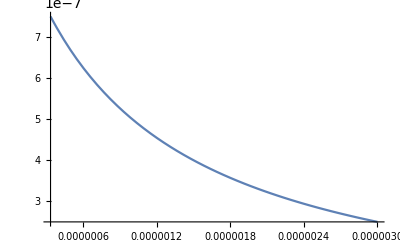

```mathematica
f=Interpolation[datasignal]
Plot[f[x],{x,3.33×10^-7,3.00×10^-6}]
```

```mathematica
Integrate[f[x],{x,step,2*step}]
```

7.19865×10^-14

```mathematica
EngineeringForm[2.204531092756365*^-12]
```

2.20453×10^-12

```mathematica
sum=0;
For[i=0,i<ga0in,i+=step,
sum=sum+Integrate[f[x],{x,i,i+step}];]
```

```mathematica
Integrate[f[x],{x,0,ga0in}]
sum
```

2.20453×10^-12

2.20453×10^-12

```mathematica
Integrate[f[x],{x,3.33*^-7,3.0*^-6}]
```

1.09886×10^-12

2.77821×10^-5

```mathematica
sum=0;
For[i=0,i<ga0in,i+=step,
If[(0.25*h0in)≤f[i]≤(0.75*h0in),
sum=sum+Integrate[f[x],{x,i,i+step}];]]
sum
```

1.06361×10^-12